## import data

```mathematica
(*Define the file paths*)
prefix ="standard_stochastic_run-2024-06-26_19-32-30";
pickleFilePath="Documents/Github/BlockScience/subspace/data/simulations/"<>prefix<>".pkl.gz";
jsonFilePath=prefix<>".json";
```

```mathematica
(*Run the Python script to convert the pickle file to JSON*)
RunProcess[{"/opt/homebrew/bin/python3.11",FileNameJoin[{NotebookDirectory[], "test/convert_pickle_to_json.py"}],pickleFilePath,jsonFilePath}]
```

<|ExitCode→0,StandardOutput→Data type: <class 'pandas.core.frame.DataFrame'>
DataFrame head:     timestep  days_passed  ...  block_time_in_seconds  max_credit_supply
0          0          0.0  ...                      6         1000000000
13         1          1.0  ...                      6         1000000000
26         2          2.0  ...                      6         1000000000
39         3          3.0  ...                      6         1000000000
52         4          4.0  ...                      6         1000000000

[5 rows x 77 columns]
,StandardError→|>

```mathematica
(*Import the JSON file*)
data=Import[FileNameJoin[{Directory[],jsonFilePath}],"JSON"];
Keys[data[[1]]]
```

{timestep,days_passed,delta_days,delta_blocks,blocks_passed,circulating_supply,user_supply,issued_supply,sum_of_stocks,earned_supply,earned_minus_burned_supply,total_supply,block_utilization,compute_fee_volume,storage_fee_volume,per_recipient_reward,proposer_bonus_reward,reward_to_proposer,reward_to_voters,reward_issuance_balance,vesting_balance,operators_balance,nominators_balance,farmers_balance,staking_pool_balance,burnt_balance,nominator_pool_shares,operator_pool_shares,block_reward,blockchain_history_size,total_space_pledged,allocated_tokens,buffer_size,average_priority_fee,average_compute_weight_per_tx,average_transaction_size,transaction_count,average_compute_weight_per_bundle,average_bundle_size,bundle_count,storage_fee_per_rewards,reference_subsidy,compute_fee_multiplier,free_space,extrinsic_length_in_bytes,storage_fee_in_shannon_per_bytes,priority_fee_volume,consensus_extrinsic_fee_volume,max_normal_weight,max_bundle_weight,target_block_fullness,adjustment_variable,target_block_delta,targeted_adjustment_parameter,tx_compute_weight,allocated_tokens_investors,allocated_tokens_founders,allocated_tokens_team,allocated_tokens_advisors,allocated_tokens_vendors,allocated_tokens_ambassadors,allocated_tokens_testnets,allocated_tokens_foundation,allocated_tokens_subspace_labs,allocated_tokens_ssl_priv_sale,community_owned_supply,cumm_rewards,cumm_storage_fees_to_farmers,cumm_compute_fees_to_farmers,simulation,subset,run,label,environmental_label,timestep_in_days,block_time_in_seconds,max_credit_supply}

```mathematica
data=Association/@data;
runs=Partition[data,502];
avgvals=Mean[runs];
```

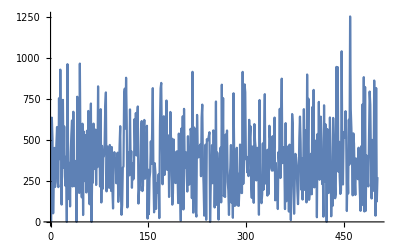

```mathematica
ListLinePlot[#["transaction_count"]/14400&/@avgvals]
```

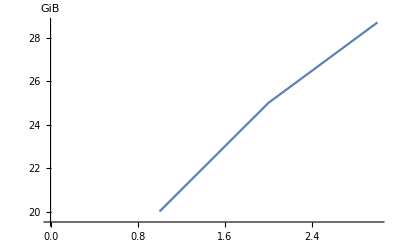

```mathematica
ListLinePlot[UnitConvert[Quantity[#["blockchain_history_size"],"Bytes"],"Gibibytes"]&/@avgvals[[;;3]],AxesLabel->Automatic]
```

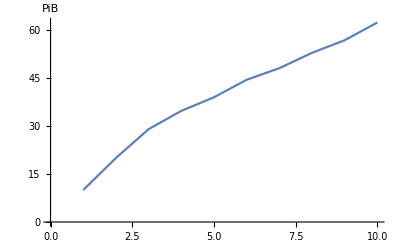

```mathematica
ListLinePlot[UnitConvert[Quantity[#["total_space_pledged"],"Bytes"],"Pebibytes"]&/@avgvals[[;;10]],AxesLabel->Automatic]
```

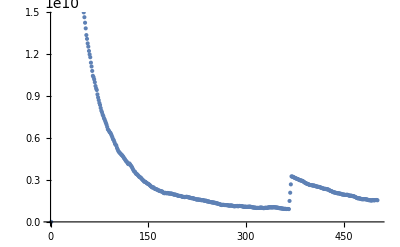

```mathematica
ListPlot[#["storage_fee_in_shannon_per_bytes"]&/@avgvals]
```

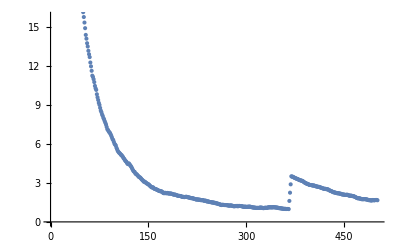

```mathematica
ListPlot[Quantity[#["storage_fee_in_shannon_per_bytes"]*1073741824/10^18,"USDollars"]&/@avgvals[[2;;]]]
```